```mathematica
NotebookEvaluate[StringJoin[NotebookDirectory[], "legendMaker.nb"]]; 
dataDir1 = StringJoin[NotebookDirectory[],  ""]; 
leg = {"Total", "Gnu", "Marmalade", "Melpa"}; 

importWithDate[n_Integer] := ({DateList[{#1[[1]], {"Year", "-", "Month", "-", "Day", "T", "Hour", ":", "Minute"}}], #1[[2]]} & ) /@ 
    Import[StringJoin[dataDir1, "main-dish.dat"], {"Data", "All", {2, n}}]; 
totalCount = importWithDate[3]; 
singleCount = importWithDate[4]; 
tarCount = importWithDate[5]; 
gnuCount = importWithDate[6]; 
marmaladeCount = importWithDate[7]; 
melpaCount = importWithDate[8]; 
melpaCount = importWithDate[9]; 
countToGrowth[list_, date_] := Module[{iv = Drop[list, (Position[#1, First[Nearest[#1, AbsoluteTime[date]]]] & )[AbsoluteTime /@ list[[All,1]]][[1,1]] - 1]}, 
    ({#1[[1]], #1[[2]] - iv[[1,2]]} & ) /@ iv]; 
today = Take[DateList[], 3];
```

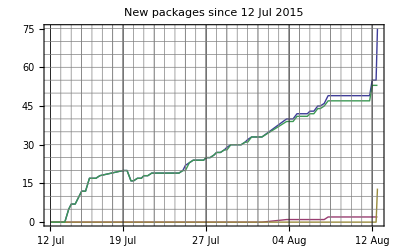
-Graphics--Graphics- | Total
-Graphics- | Gnu
-Graphics- | Marmalade
-Graphics- | Melpa

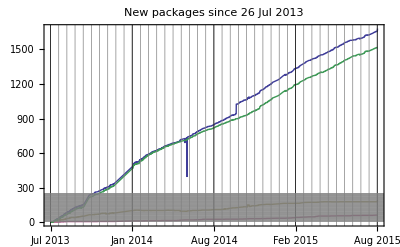
-Graphics--Graphics- | Total
-Graphics- | Gnu
-Graphics- | Marmalade
-Graphics- | Melpa

```mathematica
growthPlot[rs_, re_:today,dateFormat_:{"Day", " ", "MonthNameShort"}] := (Overlay[{#1, legendMaker[leg]}, Alignment -> {-0.7, 0.7}] & )[
    DateListPlot[(countToGrowth[#1, rs] & ) /@ {totalCount, gnuCount, marmaladeCount, melpaCount},
PlotLabel -> StringJoin["New packages since ", DateString[rs, {"Day", " ", "MonthNameShort", " ", "Year"}]],
Joined -> True,
AxesStyle -> Directive[Thickness[0.004]], 
DateTicksFormat -> dateFormat,
GridLines -> {Join[({#1, Gray} & ) /@ DateRange[rs, re, Quantity[DateDifference[rs, re]/40, "Day"]],
({#1, Black} & ) /@ DateRange[rs, re, Quantity[DateDifference[rs, re]/4, "Day"]]], ({#1, Gray} & ) /@ Array[5*#1 & , 200]},
FrameTicks -> {Automatic, {DateRange[rs, re, Quantity[DateDifference[rs, re]/4, "Day"]], None}}, Method -> {"AxesInFront" -> False}]]; 
rangeStart = DatePlus[today, {{-1, "Month"}}]; 
(* Do the plots *)
newPackagePlotMonth = growthPlot[rangeStart, today,{"Day", " ", "MonthNameShort"}]
newPackagePlotEver = growthPlot[totalCount[[1,1]], today,{"MonthNameShort", " ", "Year"}]
(Export[StringJoin[dataDir1, "2newPackagePlotEver.", #1], newPackagePlotEver, ImageSize -> 1200] & ) /@ {"pdf", "jpg", "svg", "png"}; 
(Export[StringJoin[dataDir1, "2newPackagePlotMonth.", #1], newPackagePlotMonth, ImageSize -> 1200] & ) /@ {"pdf", "jpg", "svg", "png"};
```